# Mathematica Lab 2-Properties Fourier Transform Representation

## Property-Convolution of a Continuous-Time Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *10.11.2022*

```mathematica
x[t_]:=(1/4)^t UnitStep[t];
(* This is Signal 1. *)
(* We are defining the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the TIME domain! *)
```

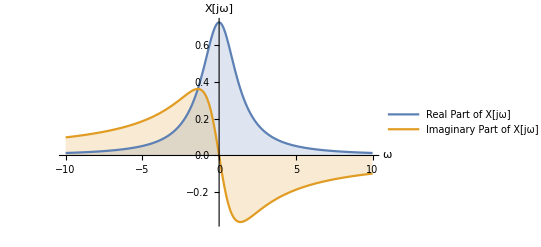

```mathematica
X[ω_]=FourierTransform[x[t],t,ω,FourierParameters->{1, -1}];
(* We are Fourier transforming the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the FREQUENCY domain! *)

PX=Plot[{Re[X[ω]],Im[X[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","X[jω]"},PlotLegends->{"Real Part of X[jω]","Imaginary Part of X[jω]"}]
(* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

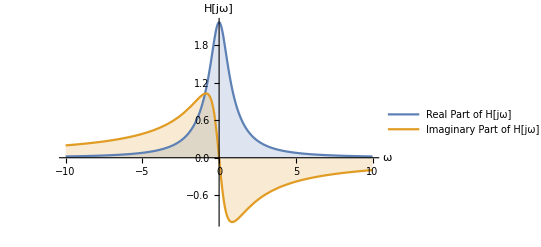

```mathematica
h[t_]:=(1/4)^t UnitStep[t]+(1/2)^t UnitStep[t];
(* This is Signal 2. *)
(* We are defining the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the TIME domain! *)

H[ω_]=FourierTransform[h[t],t,ω,FourierParameters->{1, -1}];
(* We are Fourier transforming the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the FREQUENCY domain! *)

PH=Plot[{Re[H[ω]],Im[H[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","H[jω]"},PlotLegends->{"Real Part of H[jω]","Imaginary Part of H[jω]"}](* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

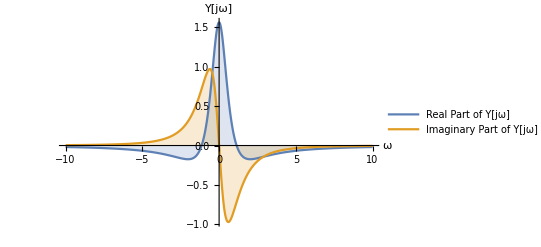

```mathematica
Y[ω_]:= X[ω]H[ω];
(* Here we use Table 4.1 to get the Fourier Transform of signal convolution. *)
(*  4.4 = Convolution=x(t)*h(t) thus X[ω]*H[ω]  *)

PY=Plot[{Re[Y[ω]],Im[Y[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","Y[jω]"},PlotLegends->{"Real Part of Y[jω]","Imaginary Part of Y[jω]"}](* We Plot the Real and Imaginary parts of the signal function,see labels in graph plot. *)
```

(4^-t (-1+2^t+t Log[2]) UnitStep[t])/Log[2]

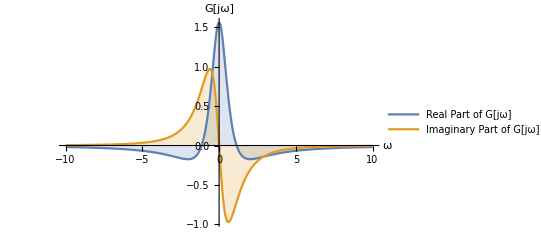

```mathematica
g[t_]=∫_(-∞)^∞ x[τ]h[t-τ]ⅆτ
(*  Here we are using convolution of the signal in the TIME domain-normally using the given formula.  *)
G[ω_]=FourierTransform[g[t],t,ω,FourierParameters->{1, -1}];
(* We are Fourier transforming the signal itself here. *)
(* It is Non-Periodic. *)
(* This signal is defiened in the FREQUENCY domain! *)

PG=Plot[{Re[G[ω]],Im[G[ω]]},{ω,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"ω","G[jω]"},PlotLegends->{"Real Part of G[jω]","Imaginary Part of G[jω]"}](* We Plot the Real and Imaginary parts of the signal function, see labels in graph plot. *)
```

```mathematica
Simplify[G[ω]==Y[ω]]   (*We prove this is true with both approaches, thus we prove the proeprty*)
```

True

```mathematica
GraphicsGrid[{{PX,PH, PY, PG}},Frame->True] (* Zoom out or scroll left to see all graphs. And we can compare G[ω] and Y[ω] visually and see they are the same, thus the property is TRUE. *)
```

-Graphics-